### Flow of complexity

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->200]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->20],2]]]

frequencyData[data_]:=Sort[Function[α,Transpose[{α,(Count[data,#]&/@α)/Length[data]}]][Union[data]],Last[#1]>Last[#2]&]

merge[data_]:=If[Length[data]>1,{{{#1[[1]],#2[[1]]},#1[[2]]+#2[[2]]},##3}&@@Sort[data,#1[[2]]<#2[[2]]&],data]

mergeAll[data_]:=If[Length[data]>1,FixedPoint[merge,data][[1,1]],{data[[1,1]]}]

HuffmanTree[data_,b_]:=mergeAll[frequencyData[Partition[data,b]]]

HassignCode[data_,l_]:=Flatten[MapIndexed[(#1->Mod[#2+1,2])&,data,{-l}]]

HgenerateCode[data_]:=HassignCode[mergeAll[frequencyData[data]],Depth[data[[1]]]]

HuffmanEncode[data_,b_]:=Module[{data1=Partition[data,b],code},code=HgenerateCode[data1];{code,Flatten[data1/.code]}]

HuffmanCodeBlock[data_,s_,lm_]:=Flatten[Module[{f,g,ct=1},(Apply[f,HuffmanTree[data,s],{-2}]/.List->g)//.{g[a_,b_]:>{Arrowed[{0},""],a,b},f[x__]:>{Arrowed[{1},""],Labeled[{x},{x}/.lm]}}]]

DiagramHuffmanEncode[data_,b_]:=Module[{c=First[HuffmanEncode[data,b]],d,fd,lm},lm=MapIndexed[#->First[#2]&,Last/@Reverse[Sort[Reverse/@frequencyData[Partition[data,b]]]]];
{Prepend[Partition[data,b],{}],Join[{HuffmanCodeBlock[data,b,lm]},List/@MapThread[Dotted,{Partition[data,b]/.c,Partition[data,b]/.lm}]]}]

GraphicsGrid[Partition[NewBCompression2DArrowed[DiagramHuffmanEncode[#1,6],51]&/@Join[Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254,250,90,150,30},Flatten[Take[#1,{27,-27}]&/@Drop[CellularAutomaton[#1,CenterArray[{1},103],50],25]]&/@{30}],2],ImageSize->700]
```

$Aborted

```mathematica
DiagramHuffmanEncode[CellularAutomaton[254,CenterArray[{1},51],25][[1]], 3][[1]]
```

{{},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
CellularAutomaton[254,CenterArray[{1},51],25][[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DiagramHuffmanEncode[#1,6]&/@CellularAutomaton[254,CenterArray[{1},51],25]
```

{{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,1,0,0,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}3,Arrowed[{1},],{1,1,1,1,0,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}3,Arrowed[{1},],{1,1,1,1,1,0}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}4,Arrowed[{1},],{1,0,0,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,0},2]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{1},],{1,1,0,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,0},2]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{1},],{0,0,0,0,0,0}1},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}4,Arrowed[{1},],{1,1,1,1,0,0}3},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}4,Arrowed[{1},],{1,1,1,1,1,0}3},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}2},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}4,Arrowed[{1},],{1,0,0,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1,0,0},4]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,0,1},3]},{Dashing[{0,Small}][{0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{1},],{1,1,0,0,0,0}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1,0,0},4]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,1},1]},{Dashing[{0,Small}][{1,0,1},3]},{Dashing[{0,Small}][{0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{1,1,1,0,0,0}3,Arrowed[{1},],{0,0,0,0,0,0}2},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0},3]},{Dashing[{0,Small}][{1,1},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}4,Arrowed[{1},],{1,1,1,1,0,0}3},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{1,0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}4,Arrowed[{1},],{1,1,1,1,1,0}3},{Dashing[{0,Small}][{1,0},2]},{Dashing[{0,Small}][{1,1,0},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1,1},3]},{Dashing[{0,Small}][{1,0},2]}}},{{{},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}3,Arrowed[{1},],{0,0,0,0,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1},2]},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,0,0},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,0,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}4,Arrowed[{1},],{0,0,1,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},2]}}},{{{},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,0,0,0,0}2,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}4,Arrowed[{1},],{0,1,1,1,1,1}3,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,1,0},4]},{Dashing[{0,Small}][{0,1,1},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,0},2]}}},{{{},{0,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,0,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,0}3,Arrowed[{1},],{1,1,1,0,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}3,Arrowed[{1},],{1,1,1,1,0,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0}},{{Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,0,0,0,1,1}3,Arrowed[{1},],{1,1,1,1,1,0}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0,0},3]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{0,1},2]}}},{{{},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,0,0,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,0,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,0,1,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{0,1,1,1,1,1}2,Arrowed[{1},],{1,1,1,1,1,1}1},{Dashing[{0,Small}][{0},2]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]},{Dashing[{0,Small}][{1},1]}}},{{{},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{g$975497[{Arrowed[{1},],{1,1,1,1,1,1}1}],{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}}}

```mathematica
(CellularAutomaton[#1,CenterArray[{1},51],25]&/@{254})
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
DiagramHuffmanEncode[#1,6]&/@(Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254})
```

{{{{},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,0,0,0,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,0,0},{0,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{Arrowed[{0},],Arrowed[{1},],{1,1,1,1,1,1}1,Arrowed[{0},],Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{1,1,1,1,0,0}3,Arrowed[{1},],{0,1,1,1,1,1}4,Arrowed[{0},],Arrowed[{0},],Arrowed[{0},],Arrowed[{1},],{0,1,0,0,0,0}9,Arrowed[{1},],{1,1,0,1,1,1}8,Arrowed[{1},],{1,1,0,0,0,0}7,Arrowed[{0},],Arrowed[{1},],{0,0,0,0,0,1}6,Arrowed[{1},],{0,0,0,1,1,1}5,Arrowed[{1},],{0,0,0,0,0,0}2},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,0,0,0},9]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,1},2]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,1},7]},{Dashing[{0,Small}][{1,0,1,1,1},5]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,1,0},6]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,0,0},3]},{Dashing[{0,Small}][{1,0,0,1},4]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{1,0,1,0,0,1},8]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]},{Dashing[{0,Small}][{0},1]}}}}

```mathematica
NewBCompression2DArrowed[x_List,width_Integer,separatordots_:True]:=Module[{fx=Flatten[x[[1]]],fy=(Flatten[#1/.{Separator->2,Labeled[u_,v_]->u,Dotted[u_,v_,w___]:>With[{z=If[{w}==={},{-1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Dotted[u[[i]]],u[[i]]],{i,Length[u]}]],Arrowed[u_,v_,w___]:>With[{z=If[{w}==={},{1},w]},Table[If[MemberQ[z,i]||MemberQ[z,i-Length[u]-1],Arrowed[u[[i]]],u[[i]]],{i,Length[u]}]]}]&)/@Rest[x],ii,jj},GraphicsRow[Insert[Graphics[{ii=0;jj=0;Table[{ii++;If[ii>width,ii=1;jj--];GrayLevel[Switch[If[IntegerQ[#1[[i]]],#1[[i]],#1[[i,1]]],0,0.85,1,0,2,0.5]],Rectangle[{ii-1,jj-1},{ii,jj}],If[separatordots&&#1[[i]]===2,{GrayLevel[0],Disk[{ii-0.5,jj-0.5},.125]},If[Head[#1[[i]]]===Dotted,{Gray,Disk[{ii-0.5,jj-0.5},.35]},If[Head[#1[[i]]]===Arrowed,{GrayLevel[0.5],Polygon[{{ii-0.6,jj-0.2},{ii-0.6,jj-0.8},{ii-0.3,jj-0.5}}]},{}]]],Directive[GrayLevel[0.15],AbsoluteThickness[0.25]],Line[{{ii-1,jj-1},{ii-1,jj},{ii,jj},{ii,jj-1},{ii-1,jj-1}}]},{i,Length[#1]}]},ImageSize->400]&/@Prepend[fy,fx],Graphics[{Arrowheads[Small],Arrow[{{0,0},{1,0}}]},ImageSize->40],2]]]

SetAttributes[Emitted,HoldAll];
Emitted[code_]:=Module[{ans={}},With[{ourEmit=Unique["Emit"]},ourEmit[val_]:=AppendTo[ans,val];
First[Hold[code]/.Emit->ourEmit];Clear[ourEmit]];ans]

LZCMunch[data_]:=Most[Module[{posi={},len=0,loc=0,s},Quiet[While[loc++<Length[data]+1,If[(s=Select[posi+=1,data[[#]]===data[[loc]]&])==={},If[len>0,Emit[{Take[data,{loc-len,loc-1}],P[loc-Last[posi],len]}]];
If[(s=Select[Flatten@Position[data,data[[loc]],{1}],#<loc&])==={},(*new element*)Emit[{{data[[loc]]}}];len=0,posi=s;
len=1],len+=1;posi=s]],Part::partw]//Emitted]]

BreakList[list_,pts_]:=Take[list,#+{0,-1}]&/@Partition[FoldList[Plus,1,pts],2,1]

FibonacciDigits[n_]:=Take@@RealDigits[N[#,N[Log10[#]+3]]&[n √5/GoldenRatio^2+1/2],GoldenRatio]

FibonacciCode[n_]:=Rest[RotateLeft[Join[FibonacciDigits[n],{0,1}]]]

FLZCEncodePieceX[bits_List]:={Arrowed[{0},""],Dotted[FibonacciCode[Length[bits]],Length[bits]],Labeled[bits,""]}

FLZCEncodePieceX[x:P[offset_,len_]]:={Arrowed[{1},""],Dotted[FibonacciCode[len],len],Labeled[FibonacciCode[offset],StringForm["⊲``⊲",offset]]}

FLZCEncodePiece[bits_List]:=Join[{0},FibonacciCode[Length[bits]],bits]

FLZCEncode[data_]:=If[Sort[#]===#&[FLZCEncodePiece/@#],First[#],Last[#]]&/@LZCMunch[data]

DiagramFLZCEncode[data_]:=Module[{c=Split[Flatten[FLZCEncode[data]],Head[#1]===Head[#2]&]/.{a__P}:>a},{BreakList[data,llen/@c],FLZCEncodePieceX/@c}]
```

```mathematica
GraphicsGrid[Partition[NewBCompression2DArrowed[DiagramFLZCEncode[#1],51]&/@Join[Flatten[CellularAutomaton[#1,CenterArray[{1},51],25]]&/@{254,250,90,150,30},Flatten[Take[#1,{27,-27}]&/@Drop[CellularAutomaton[#1,CenterArray[{1},103],50],25]]&/@{30}],2],ImageSize->850]
```

```mathematica
ArrayPlot[CellularAutomaton[254, {{1} , 0}, 30]]
```

-Graphics-

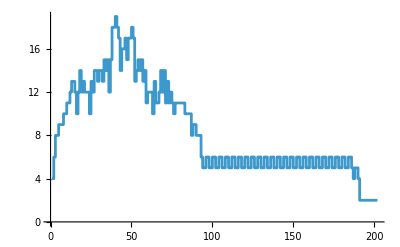

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[l1[[bmi[[1]], 1]],{{1}, 0},{200, {-25, 25}}]]
```

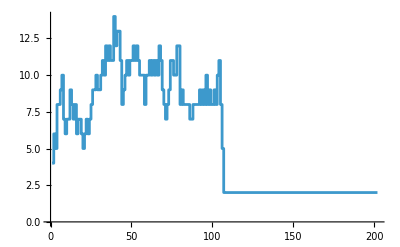
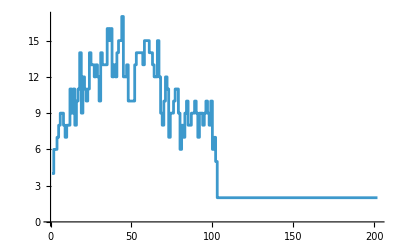
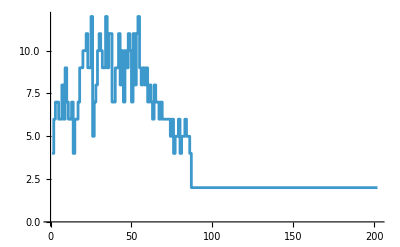
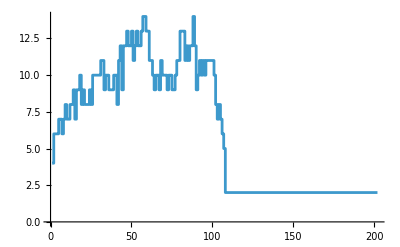
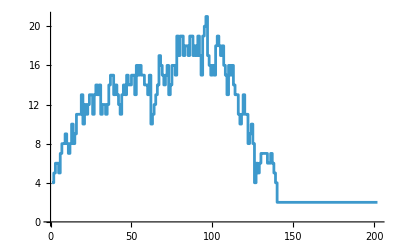
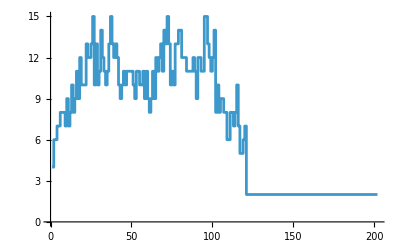
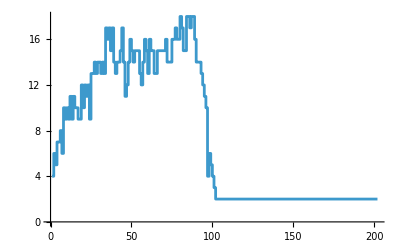
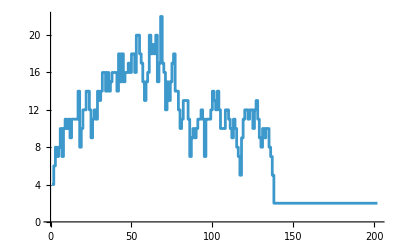
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[#,{{1}, 0},{200, {-25, 25}}]]&/@ l1[[bmi[[1;;10]], 1]]
```

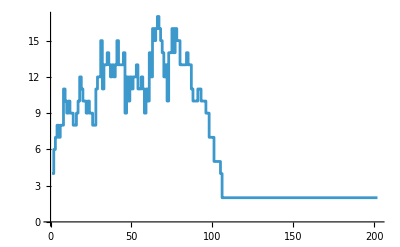
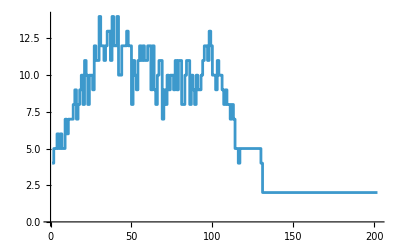
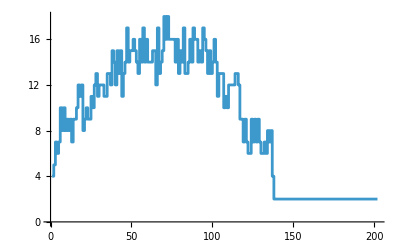
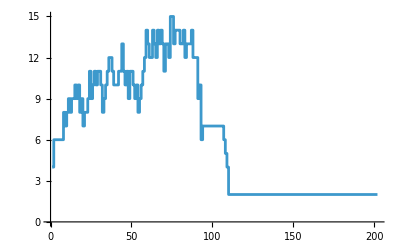
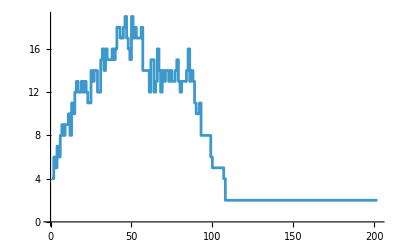
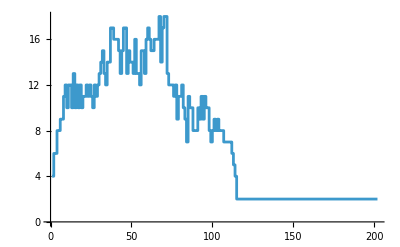
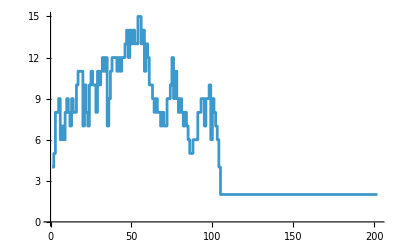
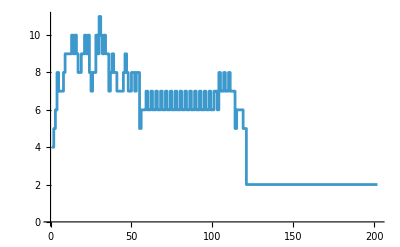

```mathematica
ListStepPlot[Length/@FLZCEncode/@CellularAutomaton[#,{{1}, 0},{200, {-25, 25}}]]&/@ {{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}}[[All, 1]]
```

```mathematica
Style[Row[Riffle[{{"[◼]", "PlotCA"}}[CellularAutomaton[First[#],{{1},0},{150,{-100,100}}],ImageSize->{Automatic,250}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}},Spacer[4]]],LineSpacing->{1.05,1.1}]
```

### Writing simplicity part

So the point is that these patterns are attractors. But they don’t just attract to white, because then they would be too short, they attract to some alternative state, which is simple enough so that it predictably lives a long time. So in a way, these patterns are solving the given problem in a much more purposeful way.

And this makes sense, because we are asking the automata to achieve a goal that is more general. It doesn’t just have to live a long finite length in the blank state, but also in other states. And because of this generality, the programs that are able to achieve that goal are more specific and less random, which we, as observers of the systems, perceive as structure.

In other words, the level of generality of the selection function will be proportional to the level of structure within the resulting adaptive system. One potential example of this is the case of embryogenesis in mammals versus in other animal groups, like amphibians.

Frogs for example, go from egg cell to tadpole and then from tadpole to frog. Importantly, the transition from tadpole to frog occurs in the wild, and therefore must be able to handle more noise. And, I suspect that this has pushed the cells to find more purposeful mechanisms for the growth and movement, of tissues within the system. And it is this mechanism that also enables amphibians to do things like regeneration. Basically, much like our perturbed automata, amphibians had to solve a the problem of dealing with perturbations

Because of this, I suspect that the evolved mechanisms for making this transition are quite purposeful. 

 Therefore, the frog cells, have to solve the problem of

I should say, that this is not the only force that influences the level of structure, for instance there are physical limitations to what the system can “build”. In many cases, there simply is no adaptive path to a structured pattern, so the automatib is forced to settle for some irreducible pattern. In our evolutions for example, the vast majority of attempts don’t result in structure, no matter how long you run the function. In other words, the

More generally, we are asking for the automata to do something that’s more specific. It doesn’t just have to live a long finite length in the blank state, but also in other environmental states. And because of this specificity, the resulting programs will be more specific, appear less random, and have more structure.

Said another way, in doing a perturbed evolution we are basically looking for a pattern that can start in many different states, and still live some long finite length. And the result was that patterns that did so successfully, had more structure.

matches the specificity of the organism. And we can use this statement to make predictions about how structured we can expect different biological systems to be.

So,

And because of this generality, the “surviving” programs will necessarily be more specific, and therefore appear more structured and purposeful.

### sense plot

```mathematica
lts = With[{aps = allperts[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts]
```

```mathematica
byidx = Partition[lts/.-Infinity->401, 3];
```

```mathematica
blt = Max/@byidx;
```

```mathematica
blt = Mean/@byidx;
```

```mathematica
blt = Min/@byidx;
```

```mathematica
blt = RandomChoice/@byidx;
```

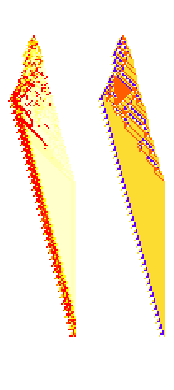

```mathematica
GraphicsRow[{
Module[{ca = CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, Abs[(# - lt)] / lt]]&)]],
PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}, {}], MeshStyle->Opacity[.1]]}]
```

```mathematica
Show[

PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}, {100, 14}->2, "Body"->True]]
```

```mathematica
Length[Catenate[bodyidxs[CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, 200]]]]
```

3353

```mathematica
Catenate[bodyidxs[CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, 200]]
```

### Testing robustness of main guy

```mathematica
Table[PlotCA[PerturbedCellularAutomaton[reg[[181, 1]], {{1}, 0}, {400, {-200, 200}}]], 30]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Weighted Rule Frequency Graph

```mathematica
init = {0, 0, 0, 0, 1, 0, 0, 0, 0};
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 0], 3, 1]
```

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{0, 0, 0}}], 6];
```

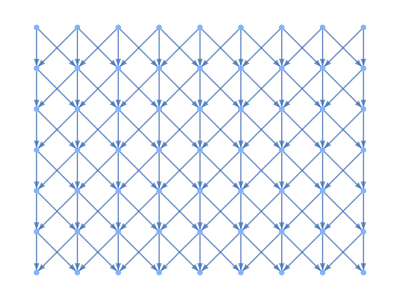

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[ArrayPlot[{#2[[2]]}, ImageSize->30,ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), VertexCoordinates->Catenate[Table[{j, i}, {i,Length[tab], 1, -1}, {j,1, Length[tab[[1]]]}]]]
```

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 3], 3, 1]
```

```mathematica
init = {3, 3, 3, 3, 2, 3, 3, 3, 3};
```

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{3, 3, 3}}], 6];
```

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&), VertexCoordinates->Catenate[Table[{j, i}, {i,Length[tab], 1, -1}, {j,1, Length[tab[[1]]]}]]]
```

-Graphics-

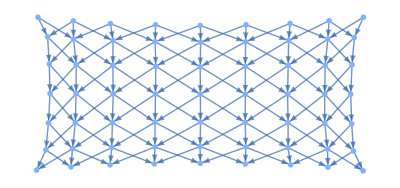

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&)]
```

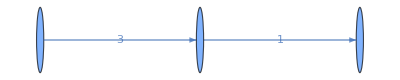

```mathematica
Graph[{1->2, 2->3}, EdgeWeight->{3, 1}, EdgeLabels->"EdgeWeight", EdgeStyle->]
```

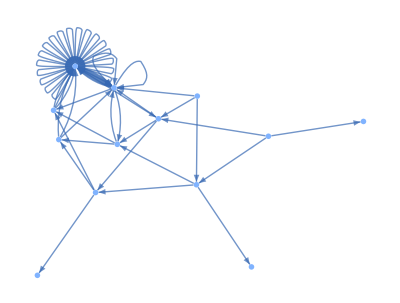

```mathematica
Graph[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]], VertexShapeFunction->(Inset[PlotCA[{#2}, ImageSize->30], #1]&), GraphLayout->"SpringElectricalEmbedding"]
```

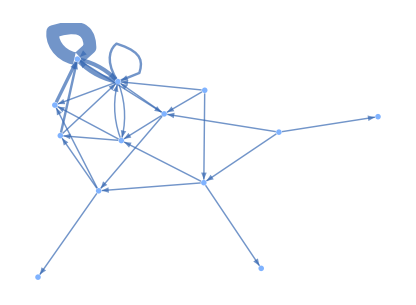

```mathematica
Graph[KeyValueMap[Style[#1, Thickness[.0025#2^.75]]&, Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]]]], VertexShapeFunction->(Inset[PlotCA[{#2}, ImageSize->30], #1]&)]
```

#### Whole pat

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 0], 3, 1]
```

```mathematica
init = CenterArray[1, 50]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
tab = NestList[nextrus, Partition[init, 3, 1],200];
```

```mathematica
Length[tab]
```

11

```mathematica
Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]]
```

<|({0,0,0}→{0,0,0})→1150,({0,0,0}→{0,0,2})→7,({0,0,0}→{0,2,1})→2,({0,0,1}→{0,0,2})→2,({0,0,1}→{0,2,1})→4,({0,0,1}→{2,1,3})→2,({0,1,0}→{0,2,1})→2,({0,1,0}→{2,1,3})→2,({0,1,0}→{1,3,0})→2,({1,0,0}→{2,1,3})→2,({1,0,0}→{1,3,0})→2,({1,0,0}→{3,0,0})→4,({0,0,0}→{1,3,0})→2,({0,0,0}→{3,0,0})→11,({0,0,0}→{0,0,3})→8,({0,0,0}→{0,3,2})→3,({0,0,2}→{0,0,3})→4,({0,0,2}→{0,3,2})→3,({0,0,2}→{3,2,1})→1,({0,2,1}→{0,3,2})→2,({0,2,1}→{3,2,1})→2,({0,2,1}→{2,1,1})→2,({2,1,3}→{3,2,1})→2,({2,1,3}→{2,1,1})→2,({2,1,3}→{1,1,0})→2,({1,3,0}→{2,1,1})→2,({1,3,0}→{1,1,0})→2,({1,3,0}→{1,0,0})→3,({3,0,0}→{1,1,0})→2,({3,0,0}→{1,0,0})→3,({3,0,0}→{0,0,0})→6,({0,0,0}→{1,0,0})→3,({0,0,3}→{0,0,0})→5,({0,0,3}→{0,0,2})→3,({0,0,3}→{0,2,3})→2,({0,3,2}→{0,0,2})→3,({0,3,2}→{0,2,3})→2,({0,3,2}→{2,3,0})→2,({3,2,1}→{0,2,3})→1,({3,2,1}→{2,3,0})→1,({3,2,1}→{3,0,3})→2,({2,1,1}→{2,3,0})→1,({2,1,1}→{3,0,3})→2,({2,1,1}→{0,3,3})→2,({1,1,0}→{3,0,3})→2,({1,1,0}→{0,3,3})→2,({1,1,0}→{3,3,0})→2,({1,0,0}→{0,3,3})→2,({1,0,0}→{3,3,0})→2,({0,0,0}→{3,3,0})→2,({0,0,2}→{3,2,3})→1,({0,2,3}→{0,3,2})→1,({0,2,3}→{3,2,3})→1,({0,2,3}→{2,3,1})→1,({2,3,0}→{3,2,3})→1,({2,3,0}→{2,3,1})→1,({2,3,0}→{3,1,2})→1,({3,0,3}→{2,3,1})→1,({3,0,3}→{3,1,2})→1,({3,0,3}→{1,2,3})→3,({0,3,3}→{3,1,2})→1,({0,3,3}→{1,2,3})→3,({0,3,3}→{2,3,0})→3,({3,3,0}→{1,2,3})→3,({3,3,0}→{2,3,0})→3,({3,3,0}→{3,0,0})→2,({3,0,0}→{2,3,0})→3,({3,0,0}→{3,0,0})→3,({0,0,3}→{0,2,2})→1,({0,3,2}→{0,2,2})→1,({0,3,2}→{2,2,2})→1,({3,2,3}→{0,2,2})→1,({3,2,3}→{2,2,2})→1,({3,2,3}→{2,2,1})→1,({2,3,1}→{2,2,2})→1,({2,3,1}→{2,2,1})→1,({2,3,1}→{2,1,1})→1,({3,1,2}→{2,2,1})→1,({3,1,2}→{2,1,1})→1,({3,1,2}→{1,1,3})→1,({1,2,3}→{2,1,1})→2,({1,2,3}→{1,1,3})→2,({1,2,3}→{1,3,0})→1,({2,3,0}→{1,1,3})→2,({2,3,0}→{1,3,0})→1,({2,3,0}→{3,0,0})→1,({3,0,0}→{1,3,0})→1,({0,0,0}→{0,3,0})→1,({0,0,2}→{0,3,0})→1,({0,0,2}→{3,0,3})→1,({0,2,2}→{0,3,0})→1,({0,2,2}→{3,0,3})→1,({0,2,2}→{0,3,3})→1,({2,2,2}→{3,0,3})→1,({2,2,2}→{0,3,3})→1,({2,2,2}→{3,3,0})→1,({2,2,1}→{0,3,3})→1,({2,2,1}→{3,3,0})→1,({2,2,1}→{3,0,0})→1,({2,1,1}→{3,3,0})→1,({2,1,1}→{3,0,0})→1,({2,1,1}→{0,0,1})→2,({1,1,3}→{3,0,0})→1,({1,1,3}→{0,0,1})→2,({1,1,3}→{0,1,0})→1,({1,3,0}→{0,0,1})→1,({1,3,0}→{0,1,0})→1,({3,0,0}→{0,1,0})→1,({0,0,3}→{0,0,1})→1,({0,3,0}→{0,0,0})→1,({0,3,0}→{0,0,1})→1,({0,3,0}→{0,1,2})→1,({3,0,3}→{0,0,1})→1,({3,0,3}→{0,1,2})→1,({0,3,3}→{0,1,2})→1,({3,3,0}→{3,0,2})→1,({3,0,0}→{3,0,2})→1,({3,0,0}→{0,2,1})→1,({0,0,1}→{3,0,2})→2,({0,0,1}→{2,1,1})→1,({0,1,2}→{0,2,1})→1,({0,1,2}→{2,1,1})→1,({0,1,2}→{1,1,3})→1,({1,2,3}→{1,3,3})→1,({2,3,0}→{1,3,3})→1,({2,3,0}→{3,3,2})→1,({3,0,2}→{1,3,3})→1,({3,0,2}→{3,3,2})→1,({3,0,2}→{3,2,1})→1,({0,2,1}→{3,3,2})→1,({0,0,2}→{3,2,0})→1,({0,2,1}→{3,2,0})→1,({0,2,1}→{2,0,0})→1,({2,1,1}→{3,2,0})→1,({2,1,1}→{2,0,0})→1,({1,1,3}→{2,0,0})→1,({1,1,3}→{0,1,1})→2,({1,3,3}→{0,0,1})→1,({1,3,3}→{0,1,1})→1,({1,3,3}→{1,1,3})→1,({3,3,2}→{0,1,1})→1,({3,3,2}→{1,1,3})→1,({3,3,2}→{1,3,0})→1,({3,2,1}→{1,1,3})→1,({3,2,1}→{1,3,0})→1,({2,1,1}→{1,3,0})→1,({3,2,0}→{0,2,3})→1,({3,2,0}→{2,3,0})→1,({3,2,0}→{3,0,2})→1,({2,0,0}→{2,3,0})→1,({2,0,0}→{3,0,2})→1,({2,0,0}→{0,2,1})→1,({0,0,1}→{2,1,0})→1,({0,1,1}→{0,2,1})→1,({0,1,1}→{2,1,0})→1,({0,1,1}→{1,0,1})→1,({1,1,3}→{2,1,0})→1,({1,1,3}→{1,0,1})→1,({1,3,0}→{1,0,1})→1,({1,3,0}→{0,1,1})→1,({1,3,0}→{1,1,2})→1,({3,0,3}→{0,1,1})→1,({3,0,3}→{1,1,2})→1,({0,3,3}→{1,1,2})→1|>

```mathematica
Select[<|a->1, b->2|>, # == 1&-> "Index"]
```

{1}

```mathematica
DeleteCases[<|a->1, b->2|>,2]
```

<|a→1|>

```mathematica
Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]]
```

<|({0,0,0}→{0,0,0})→17474,({0,0,0}→{0,0,2})→58,({0,0,0}→{0,2,1})→4,({0,0,1}→{0,0,2})→4,({0,0,1}→{0,2,1})→6,({0,0,1}→{2,1,3})→3,({0,1,0}→{0,2,1})→3,({0,1,0}→{2,1,3})→3,({0,1,0}→{1,3,0})→8,({1,0,0}→{2,1,3})→2,({1,0,0}→{1,3,0})→8,({1,0,0}→{3,0,0})→23,({0,0,0}→{1,3,0})→8,({0,0,0}→{3,0,0})→86,({0,0,0}→{0,0,3})→180,({0,0,0}→{0,3,2})→48,({0,0,2}→{0,0,3})→92,({0,0,2}→{0,3,2})→50,({0,0,2}→{3,2,1})→3,({0,2,1}→{0,3,2})→4,({0,2,1}→{3,2,1})→3,({0,2,1}→{2,1,1})→3,({2,1,3}→{3,2,1})→3,({2,1,3}→{2,1,1})→3,({2,1,3}→{1,1,0})→2,({1,3,0}→{2,1,1})→2,({1,3,0}→{1,1,0})→2,({1,3,0}→{1,0,0})→23,({3,0,0}→{1,1,0})→2,({3,0,0}→{1,0,0})→23,({3,0,0}→{0,0,0})→140,({0,0,0}→{1,0,0})→22,({0,0,3}→{0,0,0})→212,({0,0,3}→{0,0,2})→86,({0,0,3}→{0,2,3})→44,({0,3,2}→{0,0,2})→50,({0,3,2}→{0,2,3})→8,({0,3,2}→{2,3,0})→5,({3,2,1}→{0,2,3})→3,({3,2,1}→{2,3,0})→2,({3,2,1}→{3,0,3})→2,({2,1,1}→{2,3,0})→2,({2,1,1}→{3,0,3})→2,({2,1,1}→{0,3,3})→3,({1,1,0}→{3,0,3})→2,({1,1,0}→{0,3,3})→3,({1,1,0}→{3,3,0})→2,({1,0,0}→{0,3,3})→2,({1,0,0}→{3,3,0})→16,({0,0,0}→{3,3,0})→15,({0,0,2}→{3,2,3})→42,({0,2,3}→{0,3,2})→46,({0,2,3}→{3,2,3})→43,({0,2,3}→{2,3,1})→3,({2,3,0}→{3,2,3})→6,({2,3,0}→{2,3,1})→3,({2,3,0}→{3,1,2})→1,({3,0,3}→{2,3,1})→1,({3,0,3}→{3,1,2})→1,({3,0,3}→{1,2,3})→10,({0,3,3}→{3,1,2})→1,({0,3,3}→{1,2,3})→10,({0,3,3}→{2,3,0})→9,({3,3,0}→{1,2,3})→9,({3,3,0}→{2,3,0})→9,({3,3,0}→{3,0,0})→34,({3,0,0}→{2,3,0})→8,({3,0,0}→{3,0,0})→41,({0,0,3}→{0,2,2})→42,({0,3,2}→{0,2,2})→42,({0,3,2}→{2,2,2})→3,({3,2,3}→{0,2,2})→42,({3,2,3}→{2,2,2})→3,({3,2,3}→{2,2,1})→2,({2,3,1}→{2,2,2})→3,({2,3,1}→{2,2,1})→5,({2,3,1}→{2,1,1})→8,({3,1,2}→{2,2,1})→3,({3,1,2}→{2,1,1})→5,({3,1,2}→{1,1,3})→5,({1,2,3}→{2,1,1})→6,({1,2,3}→{1,1,3})→15,({1,2,3}→{1,3,0})→7,({2,3,0}→{1,1,3})→8,({2,3,0}→{1,3,0})→7,({2,3,0}→{3,0,0})→7,({3,0,0}→{1,3,0})→16,({0,0,0}→{0,3,0})→42,({0,0,2}→{0,3,0})→42,({0,0,2}→{3,0,3})→3,({0,2,2}→{0,3,0})→43,({0,2,2}→{3,0,3})→3,({0,2,2}→{0,3,3})→2,({2,2,2}→{3,0,3})→3,({2,2,2}→{0,3,3})→2,({2,2,2}→{3,3,0})→2,({2,2,1}→{0,3,3})→2,({2,2,1}→{3,3,0})→5,({2,2,1}→{3,0,0})→2,({2,1,1}→{3,3,0})→5,({2,1,1}→{3,0,0})→4,({2,1,1}→{0,0,1})→5,({1,1,3}→{3,0,0})→4,({1,1,3}→{0,0,1})→5,({1,1,3}→{0,1,0})→9,({1,3,0}→{0,0,1})→1,({1,3,0}→{0,1,0})→7,({3,0,0}→{0,1,0})→7,({0,0,3}→{0,0,1})→3,({0,3,0}→{0,0,0})→120,({0,3,0}→{0,0,1})→3,({0,3,0}→{0,1,2})→2,({3,0,3}→{0,0,1})→3,({3,0,3}→{0,1,2})→2,({0,3,3}→{0,1,2})→2,({3,3,0}→{3,0,2})→2,({3,0,0}→{3,0,2})→2,({3,0,0}→{0,2,1})→1,({0,0,1}→{3,0,2})→3,({0,0,1}→{2,1,1})→2,({0,1,2}→{0,2,1})→2,({0,1,2}→{2,1,1})→2,({0,1,2}→{1,1,3})→1,({1,2,3}→{1,3,3})→7,({2,3,0}→{1,3,3})→1,({2,3,0}→{3,3,2})→3,({3,0,2}→{1,3,3})→1,({3,0,2}→{3,3,2})→3,({3,0,2}→{3,2,1})→1,({0,2,1}→{3,3,2})→3,({0,0,2}→{3,2,0})→2,({0,2,1}→{3,2,0})→4,({0,2,1}→{2,0,0})→1,({2,1,1}→{3,2,0})→4,({2,1,1}→{2,0,0})→1,({1,1,3}→{2,0,0})→1,({1,1,3}→{0,1,1})→3,({1,3,3}→{0,0,1})→4,({1,3,3}→{0,1,1})→1,({1,3,3}→{1,1,3})→3,({3,3,2}→{0,1,1})→1,({3,3,2}→{1,1,3})→2,({3,3,2}→{1,3,0})→9,({3,2,1}→{1,1,3})→1,({3,2,1}→{1,3,0})→6,({2,1,1}→{1,3,0})→6,({3,2,0}→{0,2,3})→2,({3,2,0}→{2,3,0})→1,({3,2,0}→{3,0,2})→1,({2,0,0}→{2,3,0})→1,({2,0,0}→{3,0,2})→1,({2,0,0}→{0,2,1})→1,({0,0,1}→{2,1,0})→1,({0,1,1}→{0,2,1})→1,({0,1,1}→{2,1,0})→1,({0,1,1}→{1,0,1})→1,({1,1,3}→{2,1,0})→5,({1,1,3}→{1,0,1})→21,({1,3,0}→{1,0,1})→9,({1,3,0}→{0,1,1})→2,({1,3,0}→{1,1,2})→7,({3,0,3}→{0,1,1})→2,({3,0,3}→{1,1,2})→7,({0,3,3}→{1,1,2})→7,({0,2,3}→{2,3,3})→39,({2,3,0}→{2,3,3})→2,({3,0,2}→{2,3,3})→2,({3,0,2}→{3,2,2})→16,({0,2,1}→{3,2,2})→2,({0,2,1}→{2,2,3})→2,({2,1,0}→{3,2,2})→2,({2,1,0}→{2,2,3})→2,({2,1,0}→{2,3,1})→1,({1,0,1}→{2,2,3})→2,({1,0,1}→{2,3,1})→1,({1,0,1}→{3,1,1})→3,({0,1,1}→{2,3,1})→1,({0,1,1}→{3,1,1})→6,({0,1,1}→{1,1,1})→12,({1,1,2}→{3,1,1})→7,({1,1,2}→{1,1,1})→26,({1,1,2}→{1,1,3})→9,({1,2,3}→{1,1,1})→17,({0,3,2}→{2,2,3})→39,({3,2,3}→{2,2,3})→44,({3,2,3}→{2,3,1})→3,({2,3,3}→{2,2,3})→38,({2,3,3}→{2,3,1})→3,({2,3,3}→{3,1,3})→4,({3,3,2}→{2,3,1})→3,({3,3,2}→{3,1,3})→10,({3,2,2}→{3,1,3})→19,({3,2,2}→{1,3,0})→19,({3,2,2}→{3,0,2})→14,({2,2,3}→{1,3,0})→23,({2,2,3}→{3,0,2})→16,({2,2,3}→{0,2,1})→1,({2,3,1}→{3,0,2})→16,({2,3,1}→{0,2,1})→1,({3,1,1}→{0,2,1})→3,({3,1,1}→{2,1,1})→8,({3,1,1}→{1,1,0})→6,({1,1,1}→{2,1,1})→7,({1,1,1}→{1,1,0})→17,({1,1,1}→{1,0,1})→15,({1,1,3}→{1,1,0})→12,({0,0,2}→{3,0,0})→39,({0,2,2}→{3,0,0})→39,({0,2,2}→{0,0,2})→2,({2,2,3}→{3,0,0})→39,({2,2,3}→{0,0,2})→2,({2,2,3}→{0,2,3})→17,({2,3,1}→{0,0,2})→2,({2,3,1}→{0,2,3})→17,({2,3,1}→{2,3,1})→38,({3,1,3}→{0,2,3})→18,({3,1,3}→{2,3,1})→44,({3,1,3}→{3,1,3})→75,({1,3,0}→{2,3,1})→15,({1,3,0}→{3,1,3})→14,({1,3,0}→{1,3,2})→16,({3,0,2}→{3,1,3})→14,({3,0,2}→{1,3,2})→16,({3,0,2}→{3,2,0})→1,({0,2,1}→{1,3,2})→1,({0,2,1}→{2,0,3})→1,({2,1,1}→{2,0,3})→1,({1,1,0}→{2,0,3})→1,({1,1,0}→{3,3,1})→7,({1,0,1}→{0,3,3})→1,({1,0,1}→{3,3,1})→21,({1,0,1}→{3,1,3})→8,({0,1,0}→{3,3,1})→6,({0,1,0}→{3,1,3})→7,({1,0,0}→{3,1,3})→6,({0,3,0}→{0,0,3})→2,({3,0,0}→{0,0,3})→2,({3,0,0}→{0,3,2})→2,({0,0,2}→{3,2,2})→3,({0,2,3}→{3,2,2})→22,({0,2,3}→{2,2,3})→19,({2,3,1}→{3,2,2})→22,({2,3,1}→{2,2,3})→24,({3,1,3}→{2,2,3})→18,({1,3,2}→{2,3,1})→8,({1,3,2}→{3,1,3})→14,({1,3,2}→{1,3,3})→2,({3,2,0}→{3,1,3})→1,({3,2,0}→{1,3,3})→1,({3,2,0}→{3,3,2})→1,({2,0,3}→{1,3,3})→1,({2,0,3}→{3,3,2})→1,({2,0,3}→{3,2,3})→1,({0,3,3}→{3,3,2})→1,({0,3,3}→{3,2,3})→1,({0,3,3}→{2,3,3})→37,({3,3,1}→{3,2,3})→1,({3,3,1}→{2,3,3})→8,({3,3,1}→{3,3,1})→77,({3,1,3}→{2,3,3})→1,({3,1,3}→{3,3,1})→55,({3,1,3}→{3,1,0})→15,({1,3,0}→{3,3,1})→23,({1,3,0}→{3,1,0})→17,({3,0,0}→{3,1,0})→16,({3,2,2}→{0,2,3})→3,({3,2,2}→{2,3,0})→2,({2,2,3}→{2,3,0})→2,({3,1,3}→{3,1,1})→8,({1,3,3}→{2,3,1})→24,({1,3,3}→{3,1,1})→4,({1,3,3}→{1,1,2})→3,({3,3,2}→{3,1,1})→3,({3,3,2}→{1,1,2})→3,({3,3,2}→{1,2,3})→3,({3,2,3}→{1,1,2})→3,({3,2,3}→{1,2,3})→6,({3,2,3}→{2,3,3})→41,({2,3,3}→{1,2,3})→6,({2,3,3}→{2,3,3})→78,({2,3,3}→{3,3,3})→110,({3,3,1}→{3,3,3})→128,({3,1,0}→{3,3,3})→23,({3,1,0}→{3,3,0})→15,({1,0,0}→{3,3,3})→8,({0,2,3}→{3,3,2})→5,({0,2,3}→{2,2,1})→3,({3,1,1}→{2,2,1})→2,({3,1,1}→{1,1,1})→14,({1,1,2}→{2,1,1})→2,({2,3,3}→{1,1,3})→6,({2,3,3}→{1,3,3})→6,({3,3,3}→{1,3,3})→52,({3,3,3}→{3,3,3})→4293,({3,3,3}→{3,3,0})→98,({3,3,0}→{3,3,3})→89,({3,3,0}→{3,3,0})→109,({3,0,0}→{3,3,0})→19,({3,3,2}→{1,3,3})→1,({3,2,2}→{1,3,3})→2,({3,2,2}→{3,3,0})→3,({2,2,1}→{1,3,3})→2,({2,2,1}→{3,0,1})→3,({2,1,1}→{3,0,1})→7,({2,1,1}→{0,1,0})→2,({1,1,1}→{3,0,1})→6,({1,1,1}→{0,1,0})→2,({1,1,3}→{0,1,3})→16,({1,3,3}→{1,0,1})→9,({1,3,3}→{0,1,3})→12,({1,3,3}→{1,3,3})→53,({3,3,3}→{0,1,3})→8,({1,3,3}→{3,1,3})→60,({1,3,3}→{1,3,1})→12,({3,3,0}→{3,1,3})→10,({3,3,0}→{1,3,1})→1,({3,3,0}→{3,1,1})→3,({3,0,1}→{1,3,1})→5,({3,0,1}→{3,1,1})→8,({3,0,1}→{1,1,3})→4,({0,1,0}→{3,1,1})→1,({0,1,0}→{1,1,3})→1,({0,1,0}→{1,3,3})→2,({1,0,1}→{1,1,3})→1,({1,0,1}→{1,3,3})→14,({0,1,3}→{1,3,3})→2,({0,1,3}→{3,3,1})→13,({0,1,3}→{3,1,3})→14,({1,3,3}→{3,3,1})→37,({3,3,3}→{3,1,3})→37,({3,3,0}→{1,3,3})→9,({2,3,1}→{2,3,2})→3,({3,1,3}→{2,3,2})→3,({3,1,3}→{3,2,1})→7,({1,3,1}→{2,3,2})→3,({1,3,1}→{3,2,1})→8,({1,3,1}→{2,1,0})→4,({3,1,1}→{3,2,1})→4,({3,1,1}→{2,1,0})→4,({3,1,1}→{1,0,1})→7,({3,3,1}→{0,1,3})→3,({3,3,1}→{1,3,3})→33,({3,1,3}→{1,3,3})→12,({1,3,3}→{1,3,0})→10,({3,3,0}→{1,3,0})→10,({3,2,2}→{3,0,1})→2,({2,2,3}→{3,0,1})→3,({2,2,3}→{0,1,3})→3,({2,3,2}→{3,0,1})→3,({2,3,2}→{0,1,3})→3,({2,3,2}→{1,3,2})→2,({3,2,1}→{0,1,3})→5,({3,2,1}→{1,3,2})→2,({3,2,1}→{3,2,3})→2,({2,1,0}→{1,3,2})→2,({2,1,0}→{3,2,3})→2,({2,1,0}→{2,3,3})→3,({1,0,1}→{3,2,3})→2,({1,0,1}→{2,3,3})→4,({0,1,3}→{2,3,3})→3,({3,3,1}→{3,1,3})→25,({2,3,0}→{3,1,3})→1,({3,0,1}→{2,3,1})→3,({3,0,1}→{3,1,3})→1,({0,1,3}→{1,3,1})→4,({0,1,3}→{3,1,2})→1,({1,3,2}→{1,3,1})→1,({1,3,2}→{3,1,2})→3,({1,3,2}→{1,2,3})→3,({3,2,3}→{3,1,2})→7,({3,1,3}→{3,3,3})→51,({3,1,0}→{1,3,3})→6,({1,3,1}→{2,1,1})→5,({3,1,2}→{3,2,1})→4,({2,2,2}→{0,3,0})→1,({2,2,2}→{3,0,1})→1,({2,2,3}→{0,3,0})→2,({2,3,2}→{1,3,0})→1,({3,2,1}→{3,0,0})→2,({0,3,0}→{0,1,0})→2,({3,0,3}→{0,1,0})→1,({3,0,3}→{1,0,1})→1,({0,3,0}→{1,0,1})→1,({0,3,0}→{0,1,3})→1,({3,0,1}→{1,0,1})→1,({3,0,1}→{0,1,3})→1,({0,1,3}→{0,1,3})→1,({0,1,3}→{3,1,0})→2,({1,3,0}→{1,3,1})→2,({1,3,0}→{1,0,2})→2,({3,0,0}→{1,0,2})→2,({3,0,0}→{0,2,3})→3,({0,0,1}→{1,0,2})→2,({0,0,1}→{0,2,3})→3,({0,0,1}→{2,3,1})→3,({0,1,3}→{0,2,3})→3,({0,1,3}→{2,3,1})→3,({1,0,1}→{2,1,3})→1,({1,0,1}→{3,3,2})→1,({0,1,3}→{3,3,2})→1,({0,1,3}→{3,2,3})→1,({1,3,1}→{3,3,2})→10,({1,3,1}→{3,2,3})→6,({1,3,1}→{2,3,3})→2,({3,1,0}→{3,2,3})→2,({3,1,0}→{2,3,3})→10,({3,1,0}→{3,3,2})→4,({1,0,2}→{2,3,3})→2,({1,0,2}→{3,3,2})→5,({1,0,2}→{3,2,2})→5,({2,1,3}→{1,1,1})→2,({1,3,3}→{2,1,1})→1,({1,3,3}→{1,1,1})→1,({3,3,2}→{1,1,1})→1,({3,2,1}→{3,0,1})→4,({2,1,1}→{0,1,1})→7,({1,1,1}→{0,1,1})→9,({1,1,1}→{1,1,1})→199,({1,1,2}→{0,1,1})→3,({1,1,2}→{1,1,2})→8,({1,2,3}→{1,1,2})→9,({1,2,3}→{1,2,3})→7,({2,3,1}→{1,1,2})→9,({2,3,1}→{1,2,3})→7,({3,1,3}→{1,2,3})→7,({0,2,3}→{1,3,2})→15,({2,3,0}→{3,1,1})→1,({3,0,1}→{1,1,1})→5,({1,3,2}→{1,3,0})→15,({0,3,3}→{2,3,1})→1,({3,3,0}→{2,3,1})→1,({2,3,1}→{2,3,3})→7,({3,1,0}→{2,2,3})→6,({1,0,0}→{2,3,3})→6,({0,1,2}→{1,1,2})→1,({1,2,3}→{1,2,1})→2,({2,3,1}→{1,2,1})→2,({3,1,1}→{1,2,1})→3,({3,2,2}→{3,0,3})→5,({2,2,3}→{3,0,3})→7,({2,2,3}→{0,3,3})→42,({2,3,3}→{3,0,3})→7,({2,3,3}→{0,3,3})→42,({2,3,3}→{3,3,0})→11,({3,3,0}→{0,3,3})→6,({0,2,1}→{2,0,1})→2,({2,1,1}→{2,0,1})→2,({1,1,2}→{2,0,1})→1,({1,1,2}→{1,1,0})→2,({1,2,1}→{0,1,1})→1,({1,2,1}→{1,1,0})→2,({1,2,1}→{1,0,1})→2,({2,1,1}→{1,1,0})→2,({2,1,1}→{1,0,1})→2,({1,3,0}→{3,1,1})→11,({3,0,3}→{3,1,1})→5,({0,3,2}→{2,3,2})→1,({3,2,0}→{2,3,2})→1,({3,2,0}→{3,2,1})→2,({2,0,1}→{2,3,2})→1,({2,0,1}→{3,2,1})→2,({2,0,1}→{2,1,3})→1,({0,1,1}→{3,2,1})→2,({0,1,1}→{2,1,3})→1,({0,1,1}→{1,3,3})→1,({1,1,0}→{2,1,3})→1,({1,1,0}→{1,3,3})→13,({0,1,1}→{3,3,1})→2,({1,1,1}→{3,1,1})→10,({0,2,3}→{3,2,1})→1,({0,2,3}→{2,1,3})→1,({2,3,2}→{3,2,1})→1,({2,3,2}→{2,1,3})→1,({2,3,2}→{1,3,1})→2,({3,2,1}→{2,1,3})→1,({3,2,1}→{1,3,1})→3,({3,2,1}→{3,1,1})→3,({2,1,3}→{1,3,1})→3,({2,1,3}→{3,1,1})→3,({2,1,3}→{1,1,3})→2,({3,3,1}→{1,1,3})→1,({3,3,1}→{1,3,1})→5,({3,3,1}→{3,1,1})→15,({3,1,1}→{1,3,1})→5,({3,1,1}→{3,1,1})→14,({1,2,1}→{1,1,1})→1,({0,3,2}→{2,3,1})→1,({3,2,1}→{2,3,1})→1,({3,2,1}→{3,1,2})→1,({2,1,3}→{2,3,1})→1,({2,1,3}→{3,1,2})→1,({2,1,3}→{1,2,1})→1,({1,3,1}→{3,1,2})→1,({1,3,1}→{1,2,1})→1,({3,1,1}→{1,0,2})→3,({1,1,3}→{1,0,2})→4,({1,1,3}→{0,2,1})→2,({1,3,1}→{1,0,2})→4,({1,3,1}→{0,2,1})→2,({1,1,1}→{1,1,3})→9,({1,1,1}→{1,3,3})→7,({1,1,0}→{1,1,3})→5,({0,1,0}→{1,3,1})→2,({1,0,1}→{1,3,1})→1,({3,1,2}→{1,1,2})→1,({1,2,1}→{2,1,1})→1,({1,2,1}→{1,1,2})→1,({1,2,1}→{1,2,3})→1,({2,1,0}→{1,1,2})→1,({2,1,0}→{1,2,3})→1,({2,1,0}→{2,3,2})→1,({1,0,2}→{1,2,3})→1,({1,0,2}→{2,3,2})→1,({1,0,2}→{3,2,0})→1,({0,2,1}→{2,3,2})→1,({1,1,1}→{2,0,1})→1,({3,3,1}→{3,3,2})→9,({3,1,3}→{3,3,2})→9,({3,1,3}→{3,2,3})→9,({1,3,1}→{2,3,1})→6,({0,3,2}→{2,3,3})→1,({3,2,2}→{2,3,3})→1,({2,2,1}→{2,3,3})→1,({1,1,2}→{3,0,1})→1,({1,2,3}→{0,1,1})→1,({2,3,2}→{1,1,1})→1,({2,3,2}→{1,1,3})→1,({3,2,0}→{1,1,3})→1,({3,2,0}→{1,3,2})→1,({2,0,1}→{1,3,2})→1,({2,0,1}→{2,1,1})→1,({0,1,1}→{2,1,1})→1,({1,1,0}→{3,3,3})→6,({1,0,1}→{3,3,3})→12,({0,1,3}→{3,3,3})→9,({0,1,3}→{3,1,1})→4,({3,3,2}→{1,2,2})→4,({3,2,3}→{1,2,2})→4,({2,3,1}→{1,2,2})→4,({2,3,3}→{3,2,3})→37,({2,3,3}→{3,3,1})→5,({3,3,0}→{2,3,3})→6,({3,3,0}→{3,3,1})→1,({3,0,1}→{3,3,1})→1,({0,1,1}→{1,1,0})→1,({1,3,2}→{1,0,1})→3,({1,3,2}→{0,1,3})→3,({3,3,3}→{3,3,1})→30,({3,1,1}→{3,3,1})→20,({3,1,1}→{1,1,3})→2,({1,1,2}→{1,3,0})→1,({1,2,2}→{1,1,3})→1,({1,2,2}→{1,3,0})→4,({1,2,2}→{3,0,3})→2,({1,3,0}→{1,1,1})→3,({3,3,1}→{3,1,0})→6,({3,1,1}→{3,1,0})→6,({1,1,3}→{3,1,0})→6,({0,2,2}→{0,0,3})→37,({2,2,3}→{0,0,3})→37,({2,3,3}→{0,0,3})→36,({3,3,1}→{0,3,3})→2,({3,1,0}→{3,3,1})→1,({3,0,0}→{0,0,2})→36,({0,3,3}→{0,0,2})→36,({0,3,3}→{0,2,3})→36,({3,3,1}→{0,2,3})→1,({3,3,3}→{1,3,1})→4,({3,3,3}→{3,1,2})→4,({3,3,2}→{1,3,1})→5,({3,3,2}→{3,1,2})→4,({3,3,3}→{2,3,3})→136,({3,1,1}→{3,1,3})→5,({3,1,1}→{1,3,3})→5,({1,1,0}→{3,1,3})→5,({3,3,2}→{3,3,1})→6,({3,2,1}→{3,1,3})→4,({2,1,1}→{0,1,3})→2,({1,1,1}→{0,1,3})→2,({1,1,0}→{0,1,3})→2,({3,3,3}→{0,3,3})→34,({1,3,0}→{1,1,3})→4,({0,1,3}→{1,1,3})→3,({3,3,3}→{0,2,3})→34,({1,1,3}→{0,2,3})→2,({1,3,1}→{0,2,3})→2,({1,0,2}→{3,3,3})→2,({1,3,1}→{2,1,3})→2,({3,1,2}→{2,1,3})→2,({3,1,2}→{1,3,0})→3,({1,2,2}→{2,1,3})→2,({2,2,3}→{0,3,1})→1,({2,3,3}→{0,3,1})→1,({3,3,2}→{0,3,1})→1,({3,0,3}→{1,1,1})→2,({3,0,3}→{1,1,3})→1,({0,3,1}→{1,1,1})→1,({0,3,1}→{1,1,3})→1,({0,3,1}→{1,3,1})→1,({3,1,3}→{1,1,3})→1,({3,1,3}→{1,3,1})→1,({3,0,1}→{1,3,2})→1,({0,1,3}→{1,3,2})→1,({0,1,3}→{3,2,1})→1,({1,3,1}→{1,3,2})→1,({1,1,1}→{1,0,2})→1,({1,1,0}→{3,3,2})→1,({1,0,2}→{1,3,3})→1,({3,2,2}→{1,1,3})→1,({1,3,0}→{0,1,3})→1,({3,0,2}→{0,1,3})→1,({1,3,2}→{3,3,1})→8,({3,1,0}→{0,2,3})→1,({3,0,2}→{3,2,3})→1,({3,3,3}→{1,2,3})→1,({3,1,3}→{3,1,2})→2,({3,3,0}→{0,1,3})→1,({1,2,2}→{3,0,2})→2,({3,0,2}→{1,1,3})→1,({3,2,2}→{0,1,3})→1,({3,3,2}→{1,3,2})→1,({3,1,2}→{3,3,1})→2,({3,1,2}→{3,1,1})→1,({1,2,3}→{3,1,1})→1,({3,1,2}→{3,1,3})→1,({1,2,2}→{3,1,3})→1,({3,3,1}→{3,3,0})→1,({3,3,0}→{0,2,3})→1,({0,2,3}→{2,3,0})→1,({2,3,0}→{2,3,0})→2,({3,2,3}→{2,3,0})→1,({2,3,0}→{2,2,3})→1,({2,3,0}→{0,0,3})→1,({2,3,0}→{0,3,0})→1|>

```mathematica
KeyDrop[Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]
```

<|({0,0,0}→{0,0,2})→58,({0,0,0}→{0,2,1})→4,({0,0,1}→{0,0,2})→4,({0,0,1}→{0,2,1})→6,({0,0,1}→{2,1,3})→3,({0,1,0}→{0,2,1})→3,({0,1,0}→{2,1,3})→3,({0,1,0}→{1,3,0})→8,({1,0,0}→{2,1,3})→2,({1,0,0}→{1,3,0})→8,({1,0,0}→{3,0,0})→23,({0,0,0}→{1,3,0})→8,({0,0,0}→{3,0,0})→86,({0,0,0}→{0,0,3})→180,({0,0,0}→{0,3,2})→48,({0,0,2}→{0,0,3})→92,({0,0,2}→{0,3,2})→50,({0,0,2}→{3,2,1})→3,({0,2,1}→{0,3,2})→4,({0,2,1}→{3,2,1})→3,({0,2,1}→{2,1,1})→3,({2,1,3}→{3,2,1})→3,({2,1,3}→{2,1,1})→3,({2,1,3}→{1,1,0})→2,({1,3,0}→{2,1,1})→2,({1,3,0}→{1,1,0})→2,({1,3,0}→{1,0,0})→23,({3,0,0}→{1,1,0})→2,({3,0,0}→{1,0,0})→23,({3,0,0}→{0,0,0})→140,({0,0,0}→{1,0,0})→22,({0,0,3}→{0,0,0})→212,({0,0,3}→{0,0,2})→86,({0,0,3}→{0,2,3})→44,({0,3,2}→{0,0,2})→50,({0,3,2}→{0,2,3})→8,({0,3,2}→{2,3,0})→5,({3,2,1}→{0,2,3})→3,({3,2,1}→{2,3,0})→2,({3,2,1}→{3,0,3})→2,({2,1,1}→{2,3,0})→2,({2,1,1}→{3,0,3})→2,({2,1,1}→{0,3,3})→3,({1,1,0}→{3,0,3})→2,({1,1,0}→{0,3,3})→3,({1,1,0}→{3,3,0})→2,({1,0,0}→{0,3,3})→2,({1,0,0}→{3,3,0})→16,({0,0,0}→{3,3,0})→15,({0,0,2}→{3,2,3})→42,({0,2,3}→{0,3,2})→46,({0,2,3}→{3,2,3})→43,({0,2,3}→{2,3,1})→3,({2,3,0}→{3,2,3})→6,({2,3,0}→{2,3,1})→3,({2,3,0}→{3,1,2})→1,({3,0,3}→{2,3,1})→1,({3,0,3}→{3,1,2})→1,({3,0,3}→{1,2,3})→10,({0,3,3}→{3,1,2})→1,({0,3,3}→{1,2,3})→10,({0,3,3}→{2,3,0})→9,({3,3,0}→{1,2,3})→9,({3,3,0}→{2,3,0})→9,({3,3,0}→{3,0,0})→34,({3,0,0}→{2,3,0})→8,({3,0,0}→{3,0,0})→41,({0,0,3}→{0,2,2})→42,({0,3,2}→{0,2,2})→42,({0,3,2}→{2,2,2})→3,({3,2,3}→{0,2,2})→42,({3,2,3}→{2,2,2})→3,({3,2,3}→{2,2,1})→2,({2,3,1}→{2,2,2})→3,({2,3,1}→{2,2,1})→5,({2,3,1}→{2,1,1})→8,({3,1,2}→{2,2,1})→3,({3,1,2}→{2,1,1})→5,({3,1,2}→{1,1,3})→5,({1,2,3}→{2,1,1})→6,({1,2,3}→{1,1,3})→15,({1,2,3}→{1,3,0})→7,({2,3,0}→{1,1,3})→8,({2,3,0}→{1,3,0})→7,({2,3,0}→{3,0,0})→7,({3,0,0}→{1,3,0})→16,({0,0,0}→{0,3,0})→42,({0,0,2}→{0,3,0})→42,({0,0,2}→{3,0,3})→3,({0,2,2}→{0,3,0})→43,({0,2,2}→{3,0,3})→3,({0,2,2}→{0,3,3})→2,({2,2,2}→{3,0,3})→3,({2,2,2}→{0,3,3})→2,({2,2,2}→{3,3,0})→2,({2,2,1}→{0,3,3})→2,({2,2,1}→{3,3,0})→5,({2,2,1}→{3,0,0})→2,({2,1,1}→{3,3,0})→5,({2,1,1}→{3,0,0})→4,({2,1,1}→{0,0,1})→5,({1,1,3}→{3,0,0})→4,({1,1,3}→{0,0,1})→5,({1,1,3}→{0,1,0})→9,({1,3,0}→{0,0,1})→1,({1,3,0}→{0,1,0})→7,({3,0,0}→{0,1,0})→7,({0,0,3}→{0,0,1})→3,({0,3,0}→{0,0,0})→120,({0,3,0}→{0,0,1})→3,({0,3,0}→{0,1,2})→2,({3,0,3}→{0,0,1})→3,({3,0,3}→{0,1,2})→2,({0,3,3}→{0,1,2})→2,({3,3,0}→{3,0,2})→2,({3,0,0}→{3,0,2})→2,({3,0,0}→{0,2,1})→1,({0,0,1}→{3,0,2})→3,({0,0,1}→{2,1,1})→2,({0,1,2}→{0,2,1})→2,({0,1,2}→{2,1,1})→2,({0,1,2}→{1,1,3})→1,({1,2,3}→{1,3,3})→7,({2,3,0}→{1,3,3})→1,({2,3,0}→{3,3,2})→3,({3,0,2}→{1,3,3})→1,({3,0,2}→{3,3,2})→3,({3,0,2}→{3,2,1})→1,({0,2,1}→{3,3,2})→3,({0,0,2}→{3,2,0})→2,({0,2,1}→{3,2,0})→4,({0,2,1}→{2,0,0})→1,({2,1,1}→{3,2,0})→4,({2,1,1}→{2,0,0})→1,({1,1,3}→{2,0,0})→1,({1,1,3}→{0,1,1})→3,({1,3,3}→{0,0,1})→4,({1,3,3}→{0,1,1})→1,({1,3,3}→{1,1,3})→3,({3,3,2}→{0,1,1})→1,({3,3,2}→{1,1,3})→2,({3,3,2}→{1,3,0})→9,({3,2,1}→{1,1,3})→1,({3,2,1}→{1,3,0})→6,({2,1,1}→{1,3,0})→6,({3,2,0}→{0,2,3})→2,({3,2,0}→{2,3,0})→1,({3,2,0}→{3,0,2})→1,({2,0,0}→{2,3,0})→1,({2,0,0}→{3,0,2})→1,({2,0,0}→{0,2,1})→1,({0,0,1}→{2,1,0})→1,({0,1,1}→{0,2,1})→1,({0,1,1}→{2,1,0})→1,({0,1,1}→{1,0,1})→1,({1,1,3}→{2,1,0})→5,({1,1,3}→{1,0,1})→21,({1,3,0}→{1,0,1})→9,({1,3,0}→{0,1,1})→2,({1,3,0}→{1,1,2})→7,({3,0,3}→{0,1,1})→2,({3,0,3}→{1,1,2})→7,({0,3,3}→{1,1,2})→7,({0,2,3}→{2,3,3})→39,({2,3,0}→{2,3,3})→2,({3,0,2}→{2,3,3})→2,({3,0,2}→{3,2,2})→16,({0,2,1}→{3,2,2})→2,({0,2,1}→{2,2,3})→2,({2,1,0}→{3,2,2})→2,({2,1,0}→{2,2,3})→2,({2,1,0}→{2,3,1})→1,({1,0,1}→{2,2,3})→2,({1,0,1}→{2,3,1})→1,({1,0,1}→{3,1,1})→3,({0,1,1}→{2,3,1})→1,({0,1,1}→{3,1,1})→6,({0,1,1}→{1,1,1})→12,({1,1,2}→{3,1,1})→7,({1,1,2}→{1,1,1})→26,({1,1,2}→{1,1,3})→9,({1,2,3}→{1,1,1})→17,({0,3,2}→{2,2,3})→39,({3,2,3}→{2,2,3})→44,({3,2,3}→{2,3,1})→3,({2,3,3}→{2,2,3})→38,({2,3,3}→{2,3,1})→3,({2,3,3}→{3,1,3})→4,({3,3,2}→{2,3,1})→3,({3,3,2}→{3,1,3})→10,({3,2,2}→{3,1,3})→19,({3,2,2}→{1,3,0})→19,({3,2,2}→{3,0,2})→14,({2,2,3}→{1,3,0})→23,({2,2,3}→{3,0,2})→16,({2,2,3}→{0,2,1})→1,({2,3,1}→{3,0,2})→16,({2,3,1}→{0,2,1})→1,({3,1,1}→{0,2,1})→3,({3,1,1}→{2,1,1})→8,({3,1,1}→{1,1,0})→6,({1,1,1}→{2,1,1})→7,({1,1,1}→{1,1,0})→17,({1,1,1}→{1,0,1})→15,({1,1,3}→{1,1,0})→12,({0,0,2}→{3,0,0})→39,({0,2,2}→{3,0,0})→39,({0,2,2}→{0,0,2})→2,({2,2,3}→{3,0,0})→39,({2,2,3}→{0,0,2})→2,({2,2,3}→{0,2,3})→17,({2,3,1}→{0,0,2})→2,({2,3,1}→{0,2,3})→17,({2,3,1}→{2,3,1})→38,({3,1,3}→{0,2,3})→18,({3,1,3}→{2,3,1})→44,({3,1,3}→{3,1,3})→75,({1,3,0}→{2,3,1})→15,({1,3,0}→{3,1,3})→14,({1,3,0}→{1,3,2})→16,({3,0,2}→{3,1,3})→14,({3,0,2}→{1,3,2})→16,({3,0,2}→{3,2,0})→1,({0,2,1}→{1,3,2})→1,({0,2,1}→{2,0,3})→1,({2,1,1}→{2,0,3})→1,({1,1,0}→{2,0,3})→1,({1,1,0}→{3,3,1})→7,({1,0,1}→{0,3,3})→1,({1,0,1}→{3,3,1})→21,({1,0,1}→{3,1,3})→8,({0,1,0}→{3,3,1})→6,({0,1,0}→{3,1,3})→7,({1,0,0}→{3,1,3})→6,({0,3,0}→{0,0,3})→2,({3,0,0}→{0,0,3})→2,({3,0,0}→{0,3,2})→2,({0,0,2}→{3,2,2})→3,({0,2,3}→{3,2,2})→22,({0,2,3}→{2,2,3})→19,({2,3,1}→{3,2,2})→22,({2,3,1}→{2,2,3})→24,({3,1,3}→{2,2,3})→18,({1,3,2}→{2,3,1})→8,({1,3,2}→{3,1,3})→14,({1,3,2}→{1,3,3})→2,({3,2,0}→{3,1,3})→1,({3,2,0}→{1,3,3})→1,({3,2,0}→{3,3,2})→1,({2,0,3}→{1,3,3})→1,({2,0,3}→{3,3,2})→1,({2,0,3}→{3,2,3})→1,({0,3,3}→{3,3,2})→1,({0,3,3}→{3,2,3})→1,({0,3,3}→{2,3,3})→37,({3,3,1}→{3,2,3})→1,({3,3,1}→{2,3,3})→8,({3,3,1}→{3,3,1})→77,({3,1,3}→{2,3,3})→1,({3,1,3}→{3,3,1})→55,({3,1,3}→{3,1,0})→15,({1,3,0}→{3,3,1})→23,({1,3,0}→{3,1,0})→17,({3,0,0}→{3,1,0})→16,({3,2,2}→{0,2,3})→3,({3,2,2}→{2,3,0})→2,({2,2,3}→{2,3,0})→2,({3,1,3}→{3,1,1})→8,({1,3,3}→{2,3,1})→24,({1,3,3}→{3,1,1})→4,({1,3,3}→{1,1,2})→3,({3,3,2}→{3,1,1})→3,({3,3,2}→{1,1,2})→3,({3,3,2}→{1,2,3})→3,({3,2,3}→{1,1,2})→3,({3,2,3}→{1,2,3})→6,({3,2,3}→{2,3,3})→41,({2,3,3}→{1,2,3})→6,({2,3,3}→{2,3,3})→78,({2,3,3}→{3,3,3})→110,({3,3,1}→{3,3,3})→128,({3,1,0}→{3,3,3})→23,({3,1,0}→{3,3,0})→15,({1,0,0}→{3,3,3})→8,({0,2,3}→{3,3,2})→5,({0,2,3}→{2,2,1})→3,({3,1,1}→{2,2,1})→2,({3,1,1}→{1,1,1})→14,({1,1,2}→{2,1,1})→2,({2,3,3}→{1,1,3})→6,({2,3,3}→{1,3,3})→6,({3,3,3}→{1,3,3})→52,({3,3,3}→{3,3,3})→4293,({3,3,3}→{3,3,0})→98,({3,3,0}→{3,3,3})→89,({3,3,0}→{3,3,0})→109,({3,0,0}→{3,3,0})→19,({3,3,2}→{1,3,3})→1,({3,2,2}→{1,3,3})→2,({3,2,2}→{3,3,0})→3,({2,2,1}→{1,3,3})→2,({2,2,1}→{3,0,1})→3,({2,1,1}→{3,0,1})→7,({2,1,1}→{0,1,0})→2,({1,1,1}→{3,0,1})→6,({1,1,1}→{0,1,0})→2,({1,1,3}→{0,1,3})→16,({1,3,3}→{1,0,1})→9,({1,3,3}→{0,1,3})→12,({1,3,3}→{1,3,3})→53,({3,3,3}→{0,1,3})→8,({1,3,3}→{3,1,3})→60,({1,3,3}→{1,3,1})→12,({3,3,0}→{3,1,3})→10,({3,3,0}→{1,3,1})→1,({3,3,0}→{3,1,1})→3,({3,0,1}→{1,3,1})→5,({3,0,1}→{3,1,1})→8,({3,0,1}→{1,1,3})→4,({0,1,0}→{3,1,1})→1,({0,1,0}→{1,1,3})→1,({0,1,0}→{1,3,3})→2,({1,0,1}→{1,1,3})→1,({1,0,1}→{1,3,3})→14,({0,1,3}→{1,3,3})→2,({0,1,3}→{3,3,1})→13,({0,1,3}→{3,1,3})→14,({1,3,3}→{3,3,1})→37,({3,3,3}→{3,1,3})→37,({3,3,0}→{1,3,3})→9,({2,3,1}→{2,3,2})→3,({3,1,3}→{2,3,2})→3,({3,1,3}→{3,2,1})→7,({1,3,1}→{2,3,2})→3,({1,3,1}→{3,2,1})→8,({1,3,1}→{2,1,0})→4,({3,1,1}→{3,2,1})→4,({3,1,1}→{2,1,0})→4,({3,1,1}→{1,0,1})→7,({3,3,1}→{0,1,3})→3,({3,3,1}→{1,3,3})→33,({3,1,3}→{1,3,3})→12,({1,3,3}→{1,3,0})→10,({3,3,0}→{1,3,0})→10,({3,2,2}→{3,0,1})→2,({2,2,3}→{3,0,1})→3,({2,2,3}→{0,1,3})→3,({2,3,2}→{3,0,1})→3,({2,3,2}→{0,1,3})→3,({2,3,2}→{1,3,2})→2,({3,2,1}→{0,1,3})→5,({3,2,1}→{1,3,2})→2,({3,2,1}→{3,2,3})→2,({2,1,0}→{1,3,2})→2,({2,1,0}→{3,2,3})→2,({2,1,0}→{2,3,3})→3,({1,0,1}→{3,2,3})→2,({1,0,1}→{2,3,3})→4,({0,1,3}→{2,3,3})→3,({3,3,1}→{3,1,3})→25,({2,3,0}→{3,1,3})→1,({3,0,1}→{2,3,1})→3,({3,0,1}→{3,1,3})→1,({0,1,3}→{1,3,1})→4,({0,1,3}→{3,1,2})→1,({1,3,2}→{1,3,1})→1,({1,3,2}→{3,1,2})→3,({1,3,2}→{1,2,3})→3,({3,2,3}→{3,1,2})→7,({3,1,3}→{3,3,3})→51,({3,1,0}→{1,3,3})→6,({1,3,1}→{2,1,1})→5,({3,1,2}→{3,2,1})→4,({2,2,2}→{0,3,0})→1,({2,2,2}→{3,0,1})→1,({2,2,3}→{0,3,0})→2,({2,3,2}→{1,3,0})→1,({3,2,1}→{3,0,0})→2,({0,3,0}→{0,1,0})→2,({3,0,3}→{0,1,0})→1,({3,0,3}→{1,0,1})→1,({0,3,0}→{1,0,1})→1,({0,3,0}→{0,1,3})→1,({3,0,1}→{1,0,1})→1,({3,0,1}→{0,1,3})→1,({0,1,3}→{0,1,3})→1,({0,1,3}→{3,1,0})→2,({1,3,0}→{1,3,1})→2,({1,3,0}→{1,0,2})→2,({3,0,0}→{1,0,2})→2,({3,0,0}→{0,2,3})→3,({0,0,1}→{1,0,2})→2,({0,0,1}→{0,2,3})→3,({0,0,1}→{2,3,1})→3,({0,1,3}→{0,2,3})→3,({0,1,3}→{2,3,1})→3,({1,0,1}→{2,1,3})→1,({1,0,1}→{3,3,2})→1,({0,1,3}→{3,3,2})→1,({0,1,3}→{3,2,3})→1,({1,3,1}→{3,3,2})→10,({1,3,1}→{3,2,3})→6,({1,3,1}→{2,3,3})→2,({3,1,0}→{3,2,3})→2,({3,1,0}→{2,3,3})→10,({3,1,0}→{3,3,2})→4,({1,0,2}→{2,3,3})→2,({1,0,2}→{3,3,2})→5,({1,0,2}→{3,2,2})→5,({2,1,3}→{1,1,1})→2,({1,3,3}→{2,1,1})→1,({1,3,3}→{1,1,1})→1,({3,3,2}→{1,1,1})→1,({3,2,1}→{3,0,1})→4,({2,1,1}→{0,1,1})→7,({1,1,1}→{0,1,1})→9,({1,1,1}→{1,1,1})→199,({1,1,2}→{0,1,1})→3,({1,1,2}→{1,1,2})→8,({1,2,3}→{1,1,2})→9,({1,2,3}→{1,2,3})→7,({2,3,1}→{1,1,2})→9,({2,3,1}→{1,2,3})→7,({3,1,3}→{1,2,3})→7,({0,2,3}→{1,3,2})→15,({2,3,0}→{3,1,1})→1,({3,0,1}→{1,1,1})→5,({1,3,2}→{1,3,0})→15,({0,3,3}→{2,3,1})→1,({3,3,0}→{2,3,1})→1,({2,3,1}→{2,3,3})→7,({3,1,0}→{2,2,3})→6,({1,0,0}→{2,3,3})→6,({0,1,2}→{1,1,2})→1,({1,2,3}→{1,2,1})→2,({2,3,1}→{1,2,1})→2,({3,1,1}→{1,2,1})→3,({3,2,2}→{3,0,3})→5,({2,2,3}→{3,0,3})→7,({2,2,3}→{0,3,3})→42,({2,3,3}→{3,0,3})→7,({2,3,3}→{0,3,3})→42,({2,3,3}→{3,3,0})→11,({3,3,0}→{0,3,3})→6,({0,2,1}→{2,0,1})→2,({2,1,1}→{2,0,1})→2,({1,1,2}→{2,0,1})→1,({1,1,2}→{1,1,0})→2,({1,2,1}→{0,1,1})→1,({1,2,1}→{1,1,0})→2,({1,2,1}→{1,0,1})→2,({2,1,1}→{1,1,0})→2,({2,1,1}→{1,0,1})→2,({1,3,0}→{3,1,1})→11,({3,0,3}→{3,1,1})→5,({0,3,2}→{2,3,2})→1,({3,2,0}→{2,3,2})→1,({3,2,0}→{3,2,1})→2,({2,0,1}→{2,3,2})→1,({2,0,1}→{3,2,1})→2,({2,0,1}→{2,1,3})→1,({0,1,1}→{3,2,1})→2,({0,1,1}→{2,1,3})→1,({0,1,1}→{1,3,3})→1,({1,1,0}→{2,1,3})→1,({1,1,0}→{1,3,3})→13,({0,1,1}→{3,3,1})→2,({1,1,1}→{3,1,1})→10,({0,2,3}→{3,2,1})→1,({0,2,3}→{2,1,3})→1,({2,3,2}→{3,2,1})→1,({2,3,2}→{2,1,3})→1,({2,3,2}→{1,3,1})→2,({3,2,1}→{2,1,3})→1,({3,2,1}→{1,3,1})→3,({3,2,1}→{3,1,1})→3,({2,1,3}→{1,3,1})→3,({2,1,3}→{3,1,1})→3,({2,1,3}→{1,1,3})→2,({3,3,1}→{1,1,3})→1,({3,3,1}→{1,3,1})→5,({3,3,1}→{3,1,1})→15,({3,1,1}→{1,3,1})→5,({3,1,1}→{3,1,1})→14,({1,2,1}→{1,1,1})→1,({0,3,2}→{2,3,1})→1,({3,2,1}→{2,3,1})→1,({3,2,1}→{3,1,2})→1,({2,1,3}→{2,3,1})→1,({2,1,3}→{3,1,2})→1,({2,1,3}→{1,2,1})→1,({1,3,1}→{3,1,2})→1,({1,3,1}→{1,2,1})→1,({3,1,1}→{1,0,2})→3,({1,1,3}→{1,0,2})→4,({1,1,3}→{0,2,1})→2,({1,3,1}→{1,0,2})→4,({1,3,1}→{0,2,1})→2,({1,1,1}→{1,1,3})→9,({1,1,1}→{1,3,3})→7,({1,1,0}→{1,1,3})→5,({0,1,0}→{1,3,1})→2,({1,0,1}→{1,3,1})→1,({3,1,2}→{1,1,2})→1,({1,2,1}→{2,1,1})→1,({1,2,1}→{1,1,2})→1,({1,2,1}→{1,2,3})→1,({2,1,0}→{1,1,2})→1,({2,1,0}→{1,2,3})→1,({2,1,0}→{2,3,2})→1,({1,0,2}→{1,2,3})→1,({1,0,2}→{2,3,2})→1,({1,0,2}→{3,2,0})→1,({0,2,1}→{2,3,2})→1,({1,1,1}→{2,0,1})→1,({3,3,1}→{3,3,2})→9,({3,1,3}→{3,3,2})→9,({3,1,3}→{3,2,3})→9,({1,3,1}→{2,3,1})→6,({0,3,2}→{2,3,3})→1,({3,2,2}→{2,3,3})→1,({2,2,1}→{2,3,3})→1,({1,1,2}→{3,0,1})→1,({1,2,3}→{0,1,1})→1,({2,3,2}→{1,1,1})→1,({2,3,2}→{1,1,3})→1,({3,2,0}→{1,1,3})→1,({3,2,0}→{1,3,2})→1,({2,0,1}→{1,3,2})→1,({2,0,1}→{2,1,1})→1,({0,1,1}→{2,1,1})→1,({1,1,0}→{3,3,3})→6,({1,0,1}→{3,3,3})→12,({0,1,3}→{3,3,3})→9,({0,1,3}→{3,1,1})→4,({3,3,2}→{1,2,2})→4,({3,2,3}→{1,2,2})→4,({2,3,1}→{1,2,2})→4,({2,3,3}→{3,2,3})→37,({2,3,3}→{3,3,1})→5,({3,3,0}→{2,3,3})→6,({3,3,0}→{3,3,1})→1,({3,0,1}→{3,3,1})→1,({0,1,1}→{1,1,0})→1,({1,3,2}→{1,0,1})→3,({1,3,2}→{0,1,3})→3,({3,3,3}→{3,3,1})→30,({3,1,1}→{3,3,1})→20,({3,1,1}→{1,1,3})→2,({1,1,2}→{1,3,0})→1,({1,2,2}→{1,1,3})→1,({1,2,2}→{1,3,0})→4,({1,2,2}→{3,0,3})→2,({1,3,0}→{1,1,1})→3,({3,3,1}→{3,1,0})→6,({3,1,1}→{3,1,0})→6,({1,1,3}→{3,1,0})→6,({0,2,2}→{0,0,3})→37,({2,2,3}→{0,0,3})→37,({2,3,3}→{0,0,3})→36,({3,3,1}→{0,3,3})→2,({3,1,0}→{3,3,1})→1,({3,0,0}→{0,0,2})→36,({0,3,3}→{0,0,2})→36,({0,3,3}→{0,2,3})→36,({3,3,1}→{0,2,3})→1,({3,3,3}→{1,3,1})→4,({3,3,3}→{3,1,2})→4,({3,3,2}→{1,3,1})→5,({3,3,2}→{3,1,2})→4,({3,3,3}→{2,3,3})→136,({3,1,1}→{3,1,3})→5,({3,1,1}→{1,3,3})→5,({1,1,0}→{3,1,3})→5,({3,3,2}→{3,3,1})→6,({3,2,1}→{3,1,3})→4,({2,1,1}→{0,1,3})→2,({1,1,1}→{0,1,3})→2,({1,1,0}→{0,1,3})→2,({3,3,3}→{0,3,3})→34,({1,3,0}→{1,1,3})→4,({0,1,3}→{1,1,3})→3,({3,3,3}→{0,2,3})→34,({1,1,3}→{0,2,3})→2,({1,3,1}→{0,2,3})→2,({1,0,2}→{3,3,3})→2,({1,3,1}→{2,1,3})→2,({3,1,2}→{2,1,3})→2,({3,1,2}→{1,3,0})→3,({1,2,2}→{2,1,3})→2,({2,2,3}→{0,3,1})→1,({2,3,3}→{0,3,1})→1,({3,3,2}→{0,3,1})→1,({3,0,3}→{1,1,1})→2,({3,0,3}→{1,1,3})→1,({0,3,1}→{1,1,1})→1,({0,3,1}→{1,1,3})→1,({0,3,1}→{1,3,1})→1,({3,1,3}→{1,1,3})→1,({3,1,3}→{1,3,1})→1,({3,0,1}→{1,3,2})→1,({0,1,3}→{1,3,2})→1,({0,1,3}→{3,2,1})→1,({1,3,1}→{1,3,2})→1,({1,1,1}→{1,0,2})→1,({1,1,0}→{3,3,2})→1,({1,0,2}→{1,3,3})→1,({3,2,2}→{1,1,3})→1,({1,3,0}→{0,1,3})→1,({3,0,2}→{0,1,3})→1,({1,3,2}→{3,3,1})→8,({3,1,0}→{0,2,3})→1,({3,0,2}→{3,2,3})→1,({3,3,3}→{1,2,3})→1,({3,1,3}→{3,1,2})→2,({3,3,0}→{0,1,3})→1,({1,2,2}→{3,0,2})→2,({3,0,2}→{1,1,3})→1,({3,2,2}→{0,1,3})→1,({3,3,2}→{1,3,2})→1,({3,1,2}→{3,3,1})→2,({3,1,2}→{3,1,1})→1,({1,2,3}→{3,1,1})→1,({3,1,2}→{3,1,3})→1,({1,2,2}→{3,1,3})→1,({3,3,1}→{3,3,0})→1,({3,3,0}→{0,2,3})→1,({0,2,3}→{2,3,0})→1,({2,3,0}→{2,3,0})→2,({3,2,3}→{2,3,0})→1,({2,3,0}→{2,2,3})→1,({2,3,0}→{0,0,3})→1,({2,3,0}→{0,3,0})→1|>

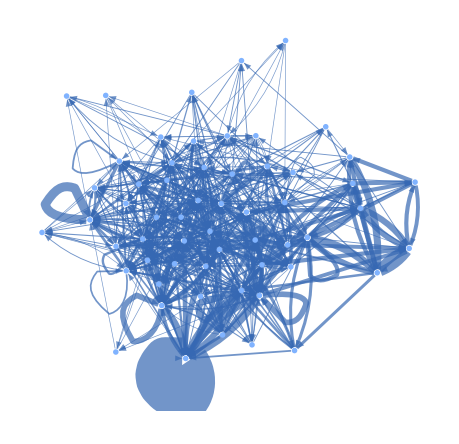

```mathematica
With[{ws =KeyDrop[Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]},  Graph[KeyValueMap[Style[#1, Thickness[.001#2^.5]]&, ws], VertexShapeFunction->(Inset[ArrayPlot[{#2}, ImageSize->30, ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), EdgeWeight->Values[ws], GraphLayout->"SpringElectricalEmbedding"]]
```

```mathematica
VertexList[]
```

```mathematica
vl  = {{0,0,0},{0,0,2},{0,2,1},{0,0,1},{2,1,3},{0,1,0},{1,3,0},{1,0,0},{3,0,0},{0,0,3},{0,3,2},{3,2,1},{2,1,1},{1,1,0},{0,2,3},{2,3,0},{3,0,3},{0,3,3},{3,3,0},{3,2,3},{2,3,1},{3,1,2},{1,2,3},{0,2,2},{2,2,2},{2,2,1},{1,1,3},{0,3,0},{0,1,2},{3,0,2},{1,3,3},{3,3,2},{3,2,0},{2,0,0},{0,1,1},{2,1,0},{1,0,1},{1,1,2},{2,3,3},{3,2,2},{2,2,3},{3,1,1},{1,1,1},{3,1,3},{1,3,2},{2,0,3},{3,3,1},{3,1,0},{3,3,3},{3,0,1},{0,1,3},{1,3,1},{2,3,2},{1,0,2},{1,2,1},{2,0,1},{1,2,2},{0,3,1}};
```

```mathematica
as = KeyDrop[Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}];
```

```mathematica
Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]]]
```

<|({0,0,0}→{0,0,0})→56|>

### Mean History Perturbed Evolution

```mathematica
With[{rus = rob[[All, 1]]},
PositionLargest[rus[[;;3]], 10, (TestCALifeTime[CellularAutomaton[#, {{1}, 0}, 200]]&)]
]
```

PositionLargest::nord3: Comparison TestCALifeTime[CellularAutomaton[#1,{{1},0},200]]& of {148929425018041907435018990866096194332,4,1} and {257533447170952912629507981728866584840,4,1} is invalid.

PositionLargest[{{182636517049556194818606469747951305480,4,1},{257533447170952912629507981728866584840,4,1},{148929425018041907435018990866096194332,4,1}},10,TestCALifeTime[CellularAutomaton[#1,{{1},0},200]]&]

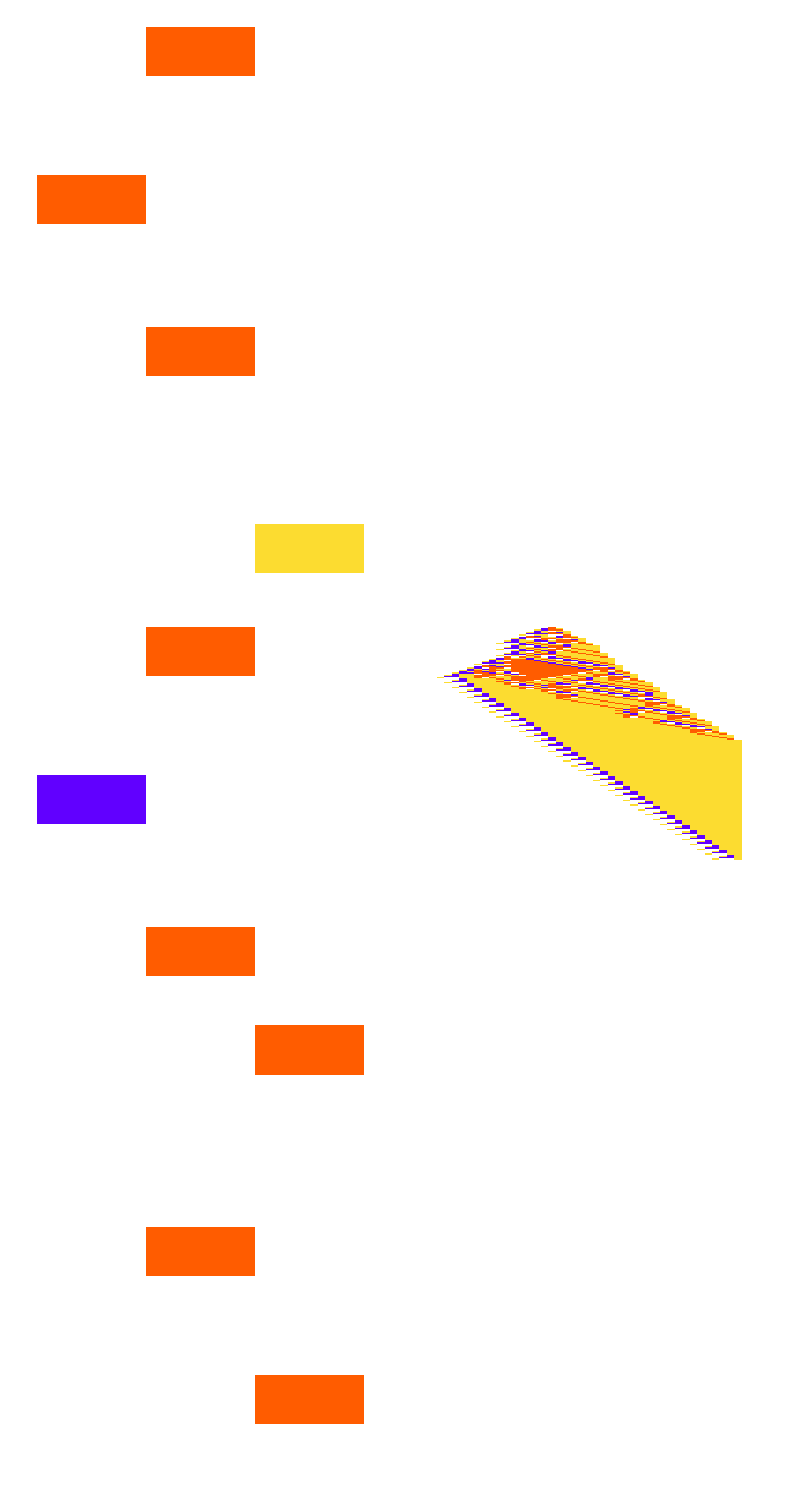

```mathematica
SeedRandom[5555];
Module[{ca = CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-15, 28}}], ss = Table[ReplacePart[Join[{{0, 1, 0}}, Table[{0, 0, 0}, 4]],{RandomInteger[{2, 5}],  RandomInteger[{1, 3}]}->RandomChoice[{1, 2, 3}]], 5]},
Graph[Append[ss,ca],#->ca&/@ss ,VertexCoordinates->Join[Table[{1, i}, {i, 1, 5}], {{3, 3}}], VertexShapeFunction->(Inset[ArrayPlot[#2, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], ImageSize->{Automatic,25 Sqrt[1+(If[# >5, #, 1]&)[TestCALifeTime[#2]]]}], #1]&), EdgeShapeFunction->"Arrow"]]
```

```mathematica
Graph[{0, 4, 1}-> reg[[43, 1]], VertexCoordinates->{{0, 0}, {1, 0}}, VertexShapeFunction->(Inset[
With[{ca = CellularAutomaton[#2, {{1}, 0}, {150, {-100, 100}}]}, 
PlotCA[ca, "Trim"->{1, 5}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,25 Sqrt[1+TestCALifeTime[ca]]}]], #1]&), EdgeShapeFunction->"Arrow"]
```

-Graphics-

### Subsection graph

```mathematica
bt = tab[[100;;200, ;;25]];
```

```mathematica
Length[tab]
```

201

```mathematica
gis = Catenate[Table[{i, j}, {i, 30, 150}, {j, 1, 20}]];
```

```mathematica
MapAt[Lighter[#, .7]&, {{"[◼]", "CustomStyleData"}}["Colors"], {All, 2}]
```

```mathematica
#1*-1-> #2&@@@{{"[◼]", "CustomStyleData"}}["Colors"]
```

```mathematica
#1*-1-> #2&@@@{{"[◼]", "CustomStyleData"}}["Colors"]
```

{0→GrayLevel[1],-1→Hue[0.06, 1, 1],-2→Hue[0.73, 1, 1],-3→Hue[0.14, 0.81, 0.99]}

```mathematica
Join[MapAt[Lighter[#, .7]&, {{"[◼]", "CustomStyleData"}}["Colors"], {All, 2}],#1*-1-> #2&@@@{{"[◼]", "CustomStyleData"}}["Colors"]]
```

{0→RGBColor[1., 1., 1.],1→RGBColor[1., 0.8079999999999999, 0.7],2→RGBColor[0.814, 0.7, 1.],3→RGBColor[0.997, 0.9585087999999999, 0.7564299999999999],0→GrayLevel[1],-1→Hue[0.06, 1, 1],-2→Hue[0.73, 1, 1],-3→Hue[0.14, 0.81, 0.99]}

```mathematica
ReplacePart[ca, #->(If[# == 0, 999, # * -1]&)[ca[[#]]]&/@ gis]
```

```mathematica
Join[MapAt[Lighter[#, .7]&, {{"[◼]", "CustomStyleData"}}["Colors"], {All, 2}],#1*-1-> #2&@@@{{"[◼]", "CustomStyleData"}}["Colors"]]
```

{0→RGBColor[1., 1., 1.],1→RGBColor[1., 0.8079999999999999, 0.7],2→RGBColor[0.814, 0.7, 1.],3→RGBColor[0.997, 0.9585087999999999, 0.7564299999999999],0→GrayLevel[1],-1→Hue[0.06, 1, 1],-2→Hue[0.73, 1, 1],-3→Hue[0.14, 0.81, 0.99]}

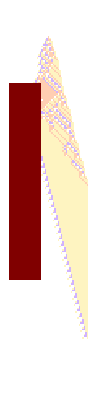

```mathematica
With[{ca = Join[#[[1]], #[[2;;,-1]]]&/@ tab}, ArrayPlot[ReplacePart[ca, #->ca[[#]]*-1&/@ gis],  ColorRules->Join[MapAt[Lighter[#, .7]&, {{"[◼]", "CustomStyleData"}}["Colors"], {All, 2}],#1*-1-> #2&@@@{{"[◼]", "CustomStyleData"}}["Colors"]]]]
```

```mathematica
Dimensions[bt]
```

{101,25,3}

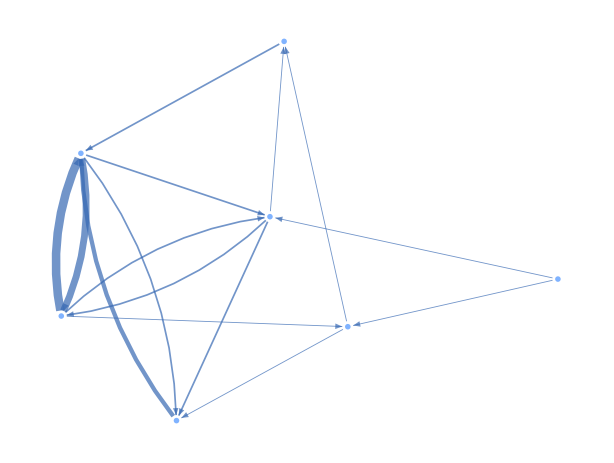

```mathematica
With[{ws =KeyDrop[Counts[Flatten[Table[bt[[i, j]]->bt[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[bt[[1]]]&], {i,1, Length[bt] - 1}, {j, 1, Length[bt[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]},  Graph[KeyValueMap[Style[#1, Thickness[.001#2]]&, ws], VertexShapeFunction->(Inset[ArrayPlot[{#2}, ImageSize->30, ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), EdgeWeight->Values[ws], GraphLayout->"SpringElectricalEmbedding"]]
```